## Logit

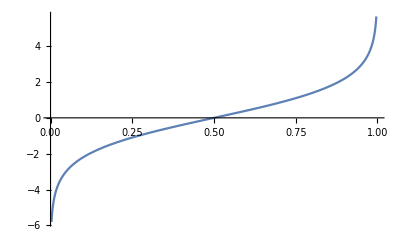

```mathematica
Plot[Log[x/(1-x)],{x, 0, 1}]
```

It is simply the inverse of the sigmoid.

## Sigmoid

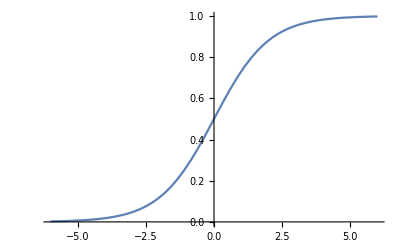

```mathematica
Plot[LogisticSigmoid[x],{x, -6, 6}]
```

So the sigmoid function forces the output in the range 0 to 1

## Softmax

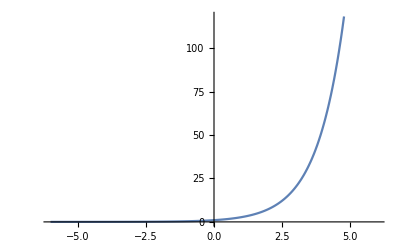

```mathematica
Plot[Exp[x],{x, -6, 6}]
```

The exponential function forces a function to the range of 0 to 1 as well and like softmax is a monotonically increasing function. The softmax converts a set of values into a categorical probability distribution. So each value in the range 0 to 1, summing to 1.

## LogSoftMax

Basically log of the softmax function. Useful when log categorical probabilities are needed.

## Negative log likelihood

This is defined just the same way that it is in statistics, where x is a probability. Maximizing x, the probability of something is the same as minimizing L. Note PyTorch’s negative log likelihood is slightly different and is designed to provide a cross-entropy loss function based on a log probabilities - for example from LogSoftMax activation layer

## Cross-Entropy Loss

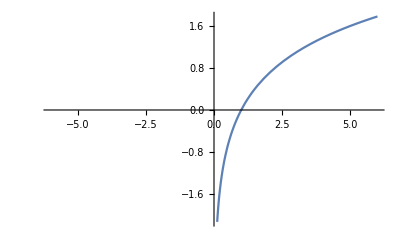

```mathematica
Plot[Log[x],{x, -6, 6}]
```

t_j is the ground truth. x_j is the categorical values. Normally a one-hot encoding is used for the t_jactivation function  and a sigmoid/softmax is applied previously to the x_j so the x_j resemble a probability distribution. In this case the probability of the correct category is the only one that contributes to the loss. The lower the probability the more negative it is. And with a mini-batch the CE loss is summed.

## Categorical Cross-Entropy loss

This is simply the Cross-Entropy loss applied on top of the SoftMax activation function with one hot coding of the ground truth.  Here p is the label for the ground truth. All the other terms have dropped to zero due to the one hot encoding.

## Binary Cross-Entropy Loss

This is simply the cross-entropy loss function applied to the sigmoid function. There are two categories. The probability of the second category is simply 1 - probability of the first category.